# E1: Introduction to Circuits Priyanka Makin Maya Fabrikant 09/15/2016

## Introduction

In this first lab, we explored basic circuits. We used a vareity of electrical components such as resistors, light bulbs, cables, DC power supply, multimeter, and oscilloscope. We first started with learning how to use the oscilloscope and measuring the resistances of the light bulb and the wire. Then we created a circuit and analyzed the relationship between voltage and current using the oscilloscope.

## Data and Calculation

```mathematica
Rsystem = 1.8; (*Bulb+Wire resistance in Ohms*)
Rwires = 0.4; (*Resistance of the wires in Ohms*)
δR = 0.1; (*Uncertainty on the Dmm in Ohms*)
Rbulb = Rsystem - Rwires (*Resistance of the bulb in Ohms*)
δRbulb = √(δR^2 + δR^2) (*Uncertainty of the resistance in Ohms*)
```

1.4

0.141421

```mathematica
Vbulb = {0.05, 0.1, 0.15, 0.2, 0.25, 0.3, 0.35, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.0, 1.1, 1.2, 1.4, 1.6, 1.8, 2.0}; (*Voltage across the bulb in Volts*)
Ibulb = {0.048, 0.093, 0.129, 0.161, 0.187, 0.209, 0.228, 0.244, 0.271, 0.291, 0.307, 0.320, 0.332, 0.343, 0.353, 0.362, 0.381, 0.399, 0.415, 0.430};(*Current through the bulb in Amps*)
VvsI = Thread[{Ibulb, Vbulb}]
```

{{0.048,0.05},{0.093,0.1},{0.129,0.15},{0.161,0.2},{0.187,0.25},{0.209,0.3},{0.228,0.35},{0.244,0.4},{0.271,0.5},{0.291,0.6},{0.307,0.7},{0.32,0.8},{0.332,0.9},{0.343,1.},{0.353,1.1},{0.362,1.2},{0.381,1.4},{0.399,1.6},{0.415,1.8},{0.43,2.}}

```mathematica
Rbulb = Vbulb/Ibulb; (*Resistance of the Bulb in Ohms*)
Pbulb = Ibulb*Vbulb; (*Power of the bulb in Watts*)
BulbData = Thread[{Vbulb, Ibulb, Rbulb, Pbulb}];
NumberForm[
Grid[Prepend[BulbData, {"Voltage (V)", "Current (A)", "Resistance (Ω)", "Power (W)"}], Frame-> All], {Infinity, 3}]
```

Voltage (V) | Current (A) | Resistance (Ω) | Power (W)
0.050 | 0.048 | 1.042 | 0.002
0.100 | 0.093 | 1.075 | 0.009
0.150 | 0.129 | 1.163 | 0.019
0.200 | 0.161 | 1.242 | 0.032
0.250 | 0.187 | 1.337 | 0.047
0.300 | 0.209 | 1.435 | 0.063
0.350 | 0.228 | 1.535 | 0.080
0.400 | 0.244 | 1.639 | 0.098
0.500 | 0.271 | 1.845 | 0.136
0.600 | 0.291 | 2.062 | 0.175
0.700 | 0.307 | 2.280 | 0.215
0.800 | 0.320 | 2.500 | 0.256
0.900 | 0.332 | 2.711 | 0.299
1.000 | 0.343 | 2.915 | 0.343
1.100 | 0.353 | 3.116 | 0.388
1.200 | 0.362 | 3.315 | 0.434
1.400 | 0.381 | 3.675 | 0.533
1.600 | 0.399 | 4.010 | 0.638
1.800 | 0.415 | 4.337 | 0.747
2.000 | 0.430 | 4.651 | 0.860

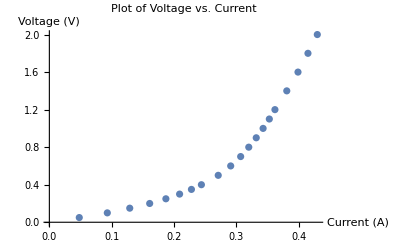

```mathematica
RvsI = Thread[{Ibulb, Rbulb}];
PvsI = Thread[{Ibulb, Pbulb}];
ListPlot[VvsI, PlotLabel-> "Plot of Voltage vs. Current", AxesLabel -> {"Current (A)", "Voltage (V)"}]
ListPlot[RvsI, PlotLabel-> "PLot of Resistance vs. Current", AxesLabel ->  {"Current (A)", "Resistance (Ω)"}]
ListPlot[PvsI, PlotLabel-> "Plot of Power vs. Current",  AxesLabel -> {"Current (A)", "Power (W)"}]
```

The plot above describes the relationship between voltage and current in the light bulb. It resembles an exponential curve.

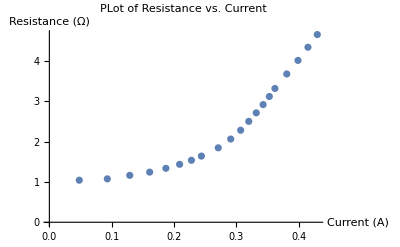

The plot above describes the relationship between resistance and current in the light bulb. It resembles an exponential curve.

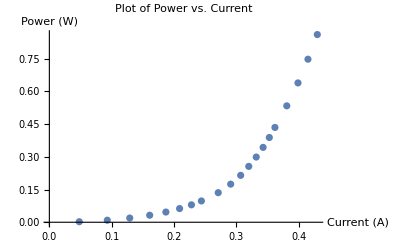

The plot above describes the relationship between power and current in the light bulb. It resembles an exponential curve.

## Conclusion

From this experiment, we can see that many things change in a circuit when we increase the voltage. By looking in the data table, we can tell that the resistance of the light bulb increases as voltage does. As the power increases and the voltage increases, the light bulb gets hotter. The maximum power dissipated was 0.860 W. This was consistent with our DMM measurements because at two volts we measured 0.43 A (P =  IV = 0.43*2  = 0.86).